```mathematica
SystemOpen@FileNameJoin[{$UserBaseDirectory,"Applications"}];
```

```mathematica
<<UtilityManager`
```

```mathematica
$SaveImagePath=NotebookDirectory[]<>"Imgs";
```

```mathematica
<<PrettyRandomColor`
```

```mathematica
SeedRandom[0];gPRC=Graphics[
Riffle[PrettyRandomColor[ColorCount->200],Disk[#,1/40]&/@RandomReal[{.1,.9},{200,2}]]
,PlotRange->{0,1},ImageSize->600]
savePNG[gPRC];
```

```mathematica
SeedRandom[0];gPRCRed=Graphics[
Riffle[PrettyRandomColor[ColorCount->200,Hue->Red],Disk[#,1/40]&/@RandomReal[{.1,.9},{200,2}]]
,PlotRange->{0,1},ImageSize->600]
savePNG[gPRCRed];
```

```mathematica
SeedRandom[0];gPRCGreen=Graphics[
Riffle[PrettyRandomColor[ColorCount->200,Hue->Green],Disk[#,1/40]&/@RandomReal[{.1,.9},{200,2}]]
,PlotRange->{0,1},ImageSize->600]
savePNG[gPRCGreen];
```

```mathematica
SeedRandom[0];gPRCBlue=Graphics[
Riffle[PrettyRandomColor[ColorCount->200,Hue->Blue],Disk[#,1/40]&/@RandomReal[{.1,.9},{200,2}]]
,PlotRange->{0,1},ImageSize->600]
savePNG[gPRCBlue];
```

```mathematica
SeedRandom[0];gPRCLight=Graphics[
Riffle[PrettyRandomColor[ColorCount->200,Luminosity->"Light"],Disk[#,1/40]&/@RandomReal[{.1,.9},{200,2}]]
,PlotRange->{0,1},ImageSize->600]
savePNG[gPRCLight];
```

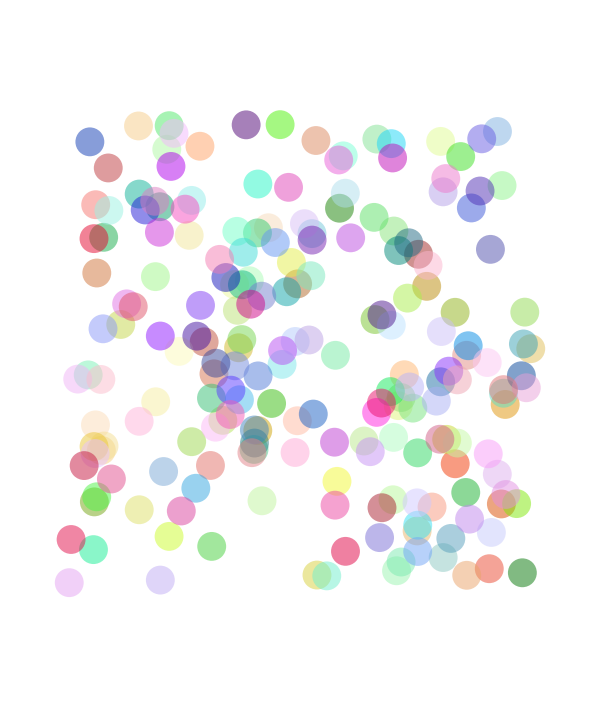

```mathematica
SeedRandom[0];gPRCOpacity=Graphics[
Riffle[PrettyRandomColor[ColorCount->200,Opacity->0.5],Disk[#,1/40]&/@RandomReal[{.1,.9},{200,2}]]
,PlotRange->{0,1},ImageSize->600]
savePNG[gPRCOpacity];
```